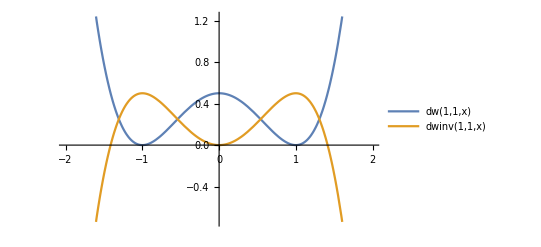

```mathematica
dwinv[a_,mu_,x_]:=-(mu^2/(2*a^2))*(x^2-a^2)^2+mu^2*a^4/(2*a^2)
dw[a_,mu_,x_]:=(mu^2/(2*a^2))*(x^2-a^2)^2

Plot[{dw[1,1,x],dwinv[1,1,x]},{x,-2,2}, PlotLegends->"Expressions"]
```

```mathematica
kink[a_,mu_,x_]:=a*Tanh[mu*x]
```

```mathematica
bounce[a_,mu_,x_]:=a*Sqrt[2]*Sech[Sqrt[2]*mu*x]
```

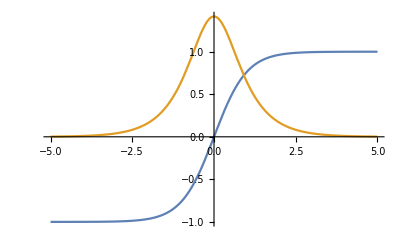

```mathematica
Plot[{kink[1,1,x],bounce[1,1,x]},{x,-5,5}]
```

```mathematica
energykink[L_,mu_,a_]:=NIntegrate[  
0.5*(D[kink[a,mu,x],x])^2+dw[a,mu,kink[a,mu,x]],{x,-L,L},AccuracyGoal->60]
```

```mathematica
energybounce[L_,mu_,a_]:=NIntegrate[  
0.5*(D[bounce[a,mu,x],x])^2+dwinv[a,mu,bounce[a,mu,x]],{x,-L,L},AccuracyGoal->60]
```

```mathematica
Sqrt[2]*energykink[100,1,1]
```

1.88562

```mathematica
energybounce[100,1,1]
```

1.88562

```mathematica
Transfer[tempe_,h_,c_,a_]:=2*Sqrt[2]*(1/(tempe^2*a^2))*h^2*(h^6/(2*c^2))*Exp[-Sqrt[2]*(1/(tempe*a))*(h^6/(2*c^2))]
freeenetransf[tempe_,h_,c_,a_]:=(Transfer[tempe,h,c,a]/(2*(1/(a^2*tempe^2))))-(0.5*tempe)*Log[2*π*a^2*tempe]
```

```mathematica
freeminimal[tempe_,h_,c_,a_]:=-(tempe/a)*Exp[-(h^6/(6*c^2))/tempe] - (-(tempe/a)*Exp[-(0.0001)/tempe])
```

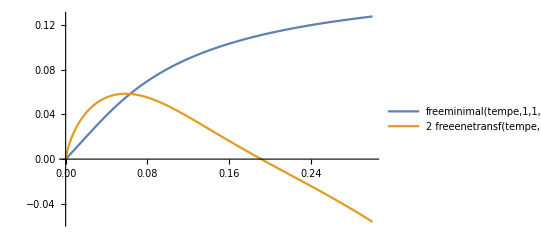

```mathematica
Plot[{freeminimal[tempe,1,1,1],2*freeenetransf[tempe,1,1,1]},{tempe,0,0.3}, PlotLegends->"Expressions"]
```

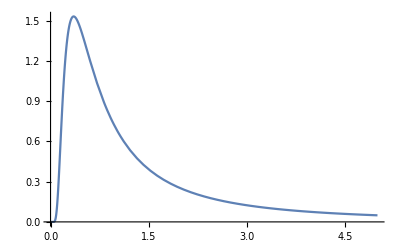

```mathematica
Plot[Transfer[tempe,1,1,1],{tempe,0,5}]
```

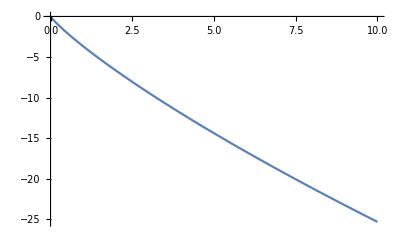

```mathematica
Plot[(0.5*tempe)*Log[2*π*0.01^2*tempe], {tempe,0,10}]
```